# Paper Plots

## Cost-Per-Timestep

```mathematica
costPerTimestep=Import["/home/twebb8/projects/cgal/c_curved_space/mathematica_tests/data_files/performance_data/cost_per_timestep_vs_num_particles_torus2308verts.txt","Data"];
```

```mathematica
TCvNData = ListPlot[costPerTimestep,PlotLabel->"Timestep Cost vs. # Particles, Torus w/2308 vertices",AxesLabel->{"# Particles", "Timestep Time (ms)"},PlotStyle->{Black,PointSize->.01}];
Clear[x]
TCvNFit = LinearModelFit[costPerTimestep,x,x];
TCvNFitPlot = Plot[TCvNFit[x],{x,0,404},PlotLabels->"Expressions"];
TCvNR2 = TCvNFit["RSquared"];
TCvNR2text = Text[StringJoin[" R^2 = ", ToString[TCvNR2]] ,{100,15000}];
TCvNR2fitText = Text[ToString[-257.921+55.6007 x],{110,18000}];
txt=Graphics[TCvNR2text];
txt2 = Graphics[TCvNR2fitText];
Show[TCvNData,TCvNFitPlot,txt,txt2]
```

-Graphics-

```mathematica
TCvNFit
```

FittedModel[-257.921+55.6007 x]

```mathematica
10000*(TCvNFit[1000]*10^-6)/24
```

23.0595

```mathematica
f1verts={{-2.7308677006373938, 0.69747676853587603, 0.98246187258845719},
{-2.6865767179563194, 0.4671866395184146, 0.96263844835467971},
{-2.2457031019966114 ,0.76380817158059355, 0.77766794715402721}};
s1 = f1verts[[2]]-f1verts[[1]];
s2 = f1verts[[3]]-f1verts[[1]];
Norm[Cross[s1,s2]]/2
```

0.0622469

## Cost for Force Evaluation vs. Particle Number

```mathematica
fcostVsNeighbors=Import["/home/twebb8/projects/cgal/c_curved_space/mathematica_tests/data_files/performance_data/force_per_target/ORIGINAL.csv","Data"];
MA01 = Import["/home/twebb8/projects/cgal/c_curved_space/mathematica_tests/data_files/performance_data/force_per_target/meanArea0146936.csv","Data"];
MA02 = Import["/home/twebb8/projects/cgal/c_curved_space/mathematica_tests/data_files/performance_data/force_per_target/meanArea026378.csv","Data"];
MA03 = Import["/home/twebb8/projects/cgal/c_curved_space/mathematica_tests/data_files/performance_data/force_per_target/meanArea0503395.csv","Data"];
complexityScales = {MA01,MA02,MA03};
fvnLegends = {"Mean Area 0.0147","Mean Area 0.02638", "Mean Area 0.05034"}
```

{Mean Area 0.0147,Mean Area 0.02638,Mean Area 0.05034}

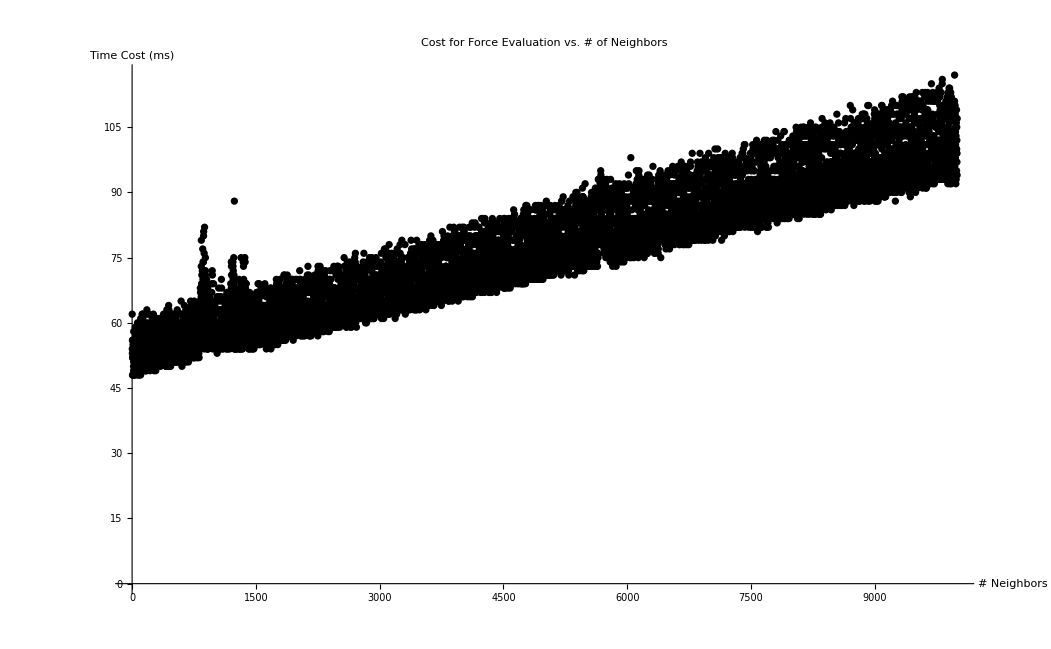

```mathematica
TCvNData = ListPlot[fcostVsNeighbors,PlotLabel->"Cost for Force Evaluation vs. # of Neighbors",AxesLabel->{"# Neighbors", "Time Cost (ms)"},PlotStyle->{Black,PointSize->.005}]
```

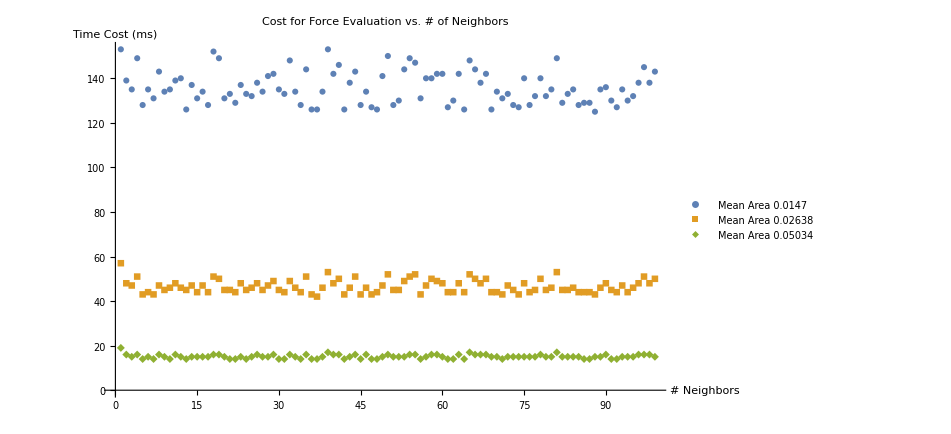

```mathematica
TCvNData = ListPlot[complexityScales,PlotLabel->"Cost for Force Evaluation vs. # of Neighbors",AxesLabel->{"# Neighbors", "Time Cost (ms)"},PlotStyle->Automatic,PlotLegends->fvnLegends,PlotMarkers->Automatic]
```

## Sequence Tree Building

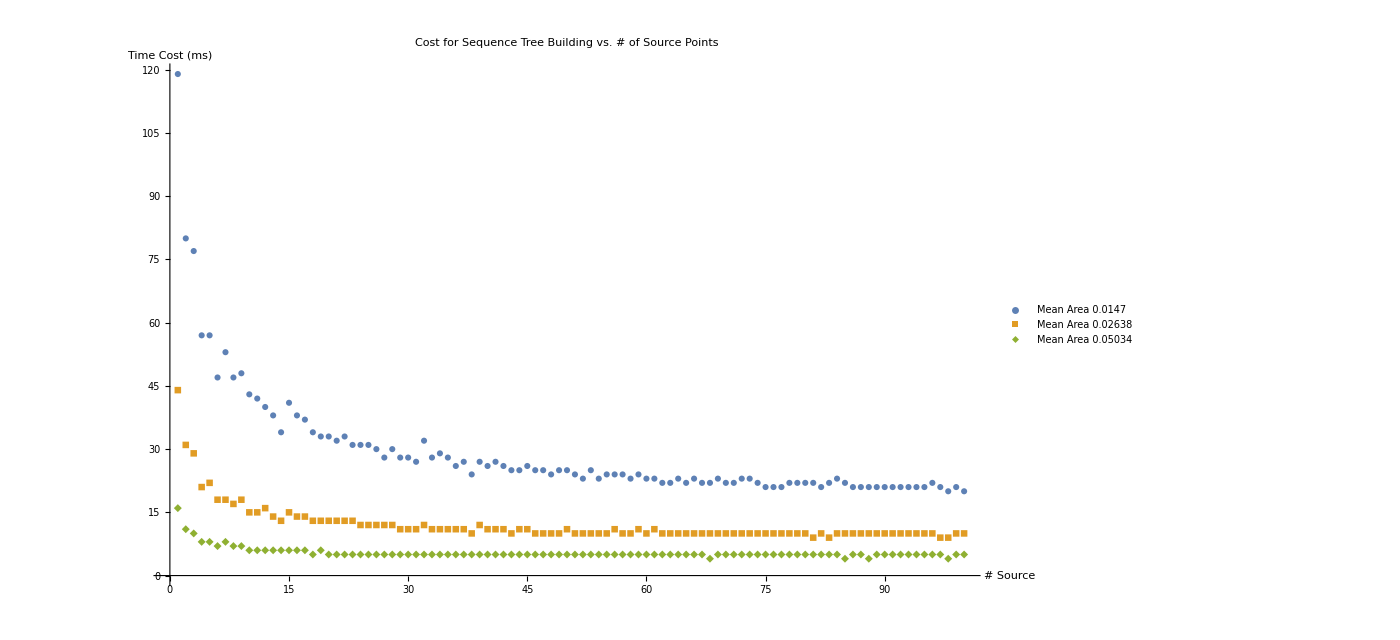

```mathematica
sqtreeRB15 = Import["/home/twebb8/projects/cgal/c_curved_space/mathematica_tests/data_files/performance_data/sqtree_rb15.csv","Data"];
sqtreeRB20 = Import["/home/twebb8/projects/cgal/c_curved_space/mathematica_tests/data_files/performance_data/sqtree_rb20.csv","Data"];
sqtreeRB30 = Import["/home/twebb8/projects/cgal/c_curved_space/mathematica_tests/data_files/performance_data/sqtree_rb30.csv","Data"];
sqtreeTimes={sqtreeRB15,sqtreeRB20,sqtreeRB30};
sqtreeLegend =  {"Mean Area 0.0147","Mean Area 0.02638", "Mean Area 0.05034"};
seqTreeTimes = ListPlot[sqtreeTimes,PlotLabel->"Cost for Sequence Tree Building vs. # of Source Points",AxesLabel->{"# Source", "Time Cost (ms)"},PlotLegends->sqtreeLegend,PlotMarkers->Automatic,PlotRange->All]
```

## Shift Tests

```mathematica
rb08testData=Import["/home/twebb8/projects/cgal/c_curved_space/mathematica_tests/data_files/performance_data/torusrb08shift.csv","Data"];
rb10testData=Import["/home/twebb8/projects/cgal/c_curved_space/mathematica_tests/data_files/performance_data/torusrb10shift.csv","Data"];
rb12testData=Import["/home/twebb8/projects/cgal/c_curved_space/mathematica_tests/data_files/performance_data/torusrb12shift.csv","Data"];
rb15testData=Import["/home/twebb8/projects/cgal/c_curved_space/mathematica_tests/data_files/performance_data/torusrb15shift.csv","Data"];
rb18testData=Import["/home/twebb8/projects/cgal/c_curved_space/mathematica_tests/data_files/performance_data/torusrb18shift.csv","Data"];
rb20testData=Import["/home/twebb8/projects/cgal/c_curved_space/mathematica_tests/data_files/performance_data/torusrb20shift.csv","Data"];
rb25testData=Import["/home/twebb8/projects/cgal/c_curved_space/mathematica_tests/data_files/performance_data/torusrb25shift.csv","Data"];
rb30testData=Import["/home/twebb8/projects/cgal/c_curved_space/mathematica_tests/data_files/performance_data/torusrb30shift.csv","Data"];
testData = {rb08testData,rb10testData,rb12testData,rb15testData,rb18testData,rb20testData,rb25testData,rb30testData};
```

```mathematica
testData[[1]][[2]]
```

{0,19454}

```mathematica
makeShiftTestIntoTable [data_]:= Table[{data[[i,1]],data[[i,2]]/(10^3)},{i,2,Length[data]}]
```

```mathematica
shiftLegends = Table[testData[[i]][[1,2]],{i,Length[testData]}]
```

{Mean Triangle Area 0.00409796,Mean Triangle Area 0.00636965,Mean Triangle Area 0.00928168,Mean Triangle Area 0.0146936,Mean Triangle Area 0.0197283,Mean Triangle Area 0.026378,Mean Triangle Area 0.0383892,Mean Triangle Area 0.0503395}

```mathematica
shiftPlottables=Table[makeShiftTestIntoTable[testData[[i]]],{i,Length[testData]}];
```

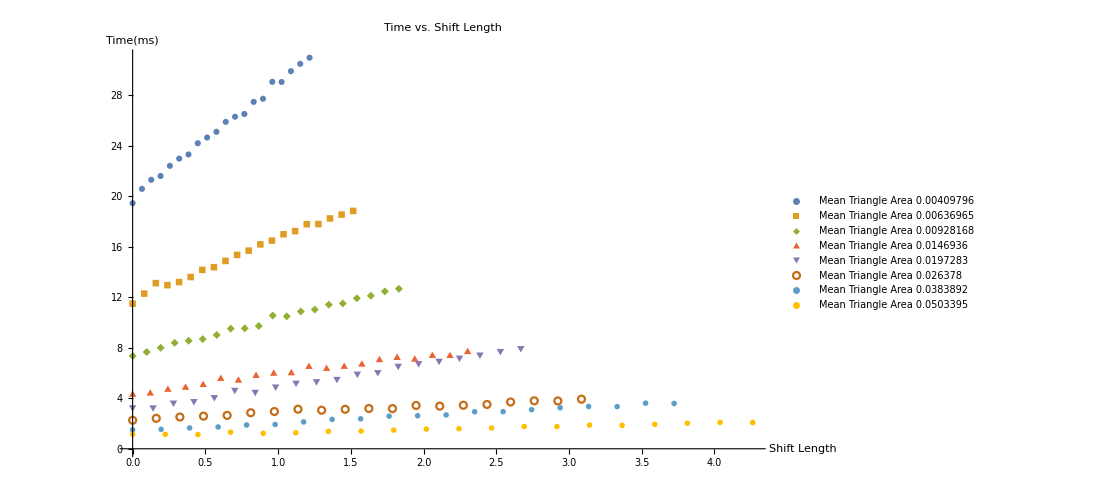

```mathematica
shiftDataPlots =ListPlot[shiftPlottables,PlotRange->All,PlotMarkers->Automatic,AxesLabel->{"Shift Length","Time(ms)"},PlotLegends->shiftLegends,PlotLabel->"Time vs. Shift Length"]
```